```mathematica
4
```

```mathematica
ut[us_,uh_,z_,θ_,μ_,q_]:=NDSolveValue[{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ)))+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]==us,u'[0]==0},u,{t,0.01,5},Method->"BDF"];
ut1[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut[us,uh,z,θ,μ,q][t1];
ut[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]][0.5]
ut1[0.5,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]
```

```mathematica
dfu[t1_,us_,uh_,z_,θ_,μ_,q_]:=D[ut[us,uh,z,θ,μ,q][t],t]/.{t->t1};
pu[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut1[t1,us,uh,z,θ,μ,q]^(θ/2-1)dfu[t1,us,uh,z,θ,μ,q]/Sqrt[ut1[t1,us,uh,z,θ,μ,q]^(2-2z)f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]^3-dfu[t1,us,uh,z,θ,μ,q]^2f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]];
βpu[t1_,us_,uh_,z_,θ_,μ_,q_]:=pu[t1,us,uh,z,θ,μ,q]/((ut1[t1,us,uh,z,θ,μ,q]*(ut1[t1,us,uh,z,θ,μ,q]/uh)^(z-θ)*(-2-z+θ))/uh^2+(ut1[t1,us,uh,z,θ,μ,q]^(1+2*z-2*θ)*uh^(-2*z+2*θ)*(-z+θ)*(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(1+z-θ)+(ut1[t1,us,uh,z,θ,μ,q]/uh)^θ*(-2-z+θ))*μ^2)/(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(-2+θ)));Show[
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.5qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],1.02qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],1.5qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],2.0qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,u},PlotRange->{{0,5},{0,1}}
]
```

```mathematica
f[u_,uh_,z_,θ_,μ_]:=1-(u/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ)u^(2z-2θ+2)/uh^(2z-2θ)(1-(u/uh)^(θ-z))
```

```mathematica
qcrit[us_,uh_,z_,θ_,μ_]:=us^(θ/2-z)Sqrt[f[us,uh,z,θ,μ]]/μ/(1-(us/uh)^(z-θ));
μext[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/(z-θ)/uh;
```

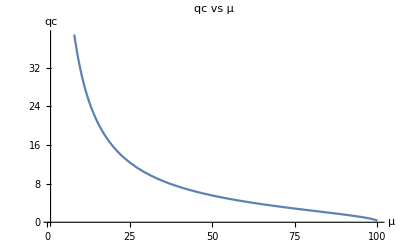

```mathematica
Plot[qcrit[0.1,1,3,1,μ],{μ,1,100},PlotLabel->"qc vs μ",AxesLabel->{μ,qc}]
```

```mathematica
ut[us_,uh_,z_,θ_,μ_,q_]:=NDSolveValue[{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ)))+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]==us,u'[0]==0},u,{t,0.01,5},Method->"ExplicitRungeKutta"];
ut1[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut[us,uh,z,θ,μ,q][t1];
ut[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]][0.5]
ut1[0.5,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]
```

0.685807

0.685807

```mathematica
dfu[t1_,us_,uh_,z_,θ_,μ_,q_]:=D[ut[us,uh,z,θ,μ,q][t],t]/.{t->t1};
pu[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut1[t1,us,uh,z,θ,μ,q]^(θ/2-1)dfu[t1,us,uh,z,θ,μ,q]/Sqrt[ut1[t1,us,uh,z,θ,μ,q]^(2-2z)f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]^3-dfu[t1,us,uh,z,θ,μ,q]^2f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]];
βpu[t1_,us_,uh_,z_,θ_,μ_,q_]:=pu[t1,us,uh,z,θ,μ,q]/((ut1[t1,us,uh,z,θ,μ,q]*(ut1[t1,us,uh,z,θ,μ,q]/uh)^(z-θ)*(-2-z+θ))/uh^2+(ut1[t1,us,uh,z,θ,μ,q]^(1+2*z-2*θ)*uh^(-2*z+2*θ)*(-z+θ)*(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(1+z-θ)+(ut1[t1,us,uh,z,θ,μ,q]/uh)^θ*(-2-z+θ))*μ^2)/(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(-2+θ)));
```

```mathematica
FindRoot[
10==qcrit[0.1,1,2.23,θ,0.75μext[1,2.23,θ]],{θ,0.4}
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{θ→1.73703}

```mathematica
(* z = 2.23 is the largest value of z for which theta_critical exists. *)
```

```mathematica
ut1[0.5,0.1,1,3,0.5,0.75μext[1,3,0.5],10]
```

0.913474-5.04232×10^-13 ⅈ

```mathematica
pu[0.5,0.1,1,3,0.5,0.75μext[1,3,0.5],10]
```

2300.67+1.46352 ⅈ

```mathematica
Table[{i,pu[i,0.1,1,3,0.5,0.75μext[1,3,0.5],10]//Abs//Log},{i,0.01,2,0.05}]
```

{{0.01,3.99718},{0.06,5.28116},{0.11,5.80361},{0.16,6.18056},{0.21,6.49097},{0.26,6.76067},{0.31,6.99973},{0.36,7.21924},{0.41,7.41446},{0.46,7.6},{0.51,7.7702},{0.56,7.93058},{0.61,8.09767},{0.66,8.21626},{0.71,8.3832},{0.76,8.49491},{0.81,8.59568},{0.86,8.69246},{0.91,8.7953},{0.96,8.88948},{1.01,8.97794},{1.06,9.09186},{1.11,9.22633},{1.16,9.43089},{1.21,9.42937},{1.26,9.34332},{1.31,9.5645},{1.36,9.81258},{1.41,9.51412},{1.46,9.92234},{1.51,9.76847},{1.56,9.90039},{1.61,10.2122},{1.66,9.90941},{1.71,10.6524},{1.76,10.0108},{1.81,10.6954},{1.86,10.2718},{1.91,10.2607},{1.96,10.7715}}

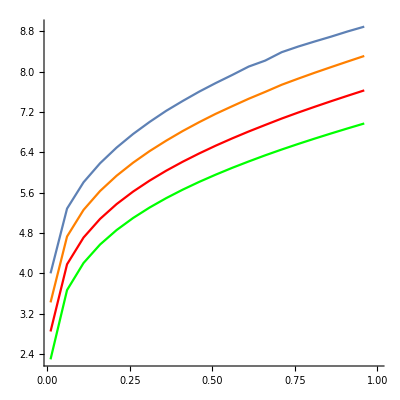

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,3,0.5,0.75μext[1,3,0.5],10]//Abs//Log},{i,0.01,1,0.05}]],
ListLinePlot[Table[{i,pu[i,0.1,1,3,1.0,0.75μext[1,3,1.0],10]//Abs//Log},{i,0.01,1,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,pu[i,0.1,1,3,1.5,0.75μext[1,3,1.5],10]//Abs//Log},{i,0.01,1,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pu[i,0.1,1,3,1.99,0.75μext[1,3,1.99],10]//Abs//Log},{i,0.01,1,0.05}],PlotStyle->Green],
PlotRange->{{0.01,1},All},AxesOrigin->{0,0},AspectRatio->1
]
```

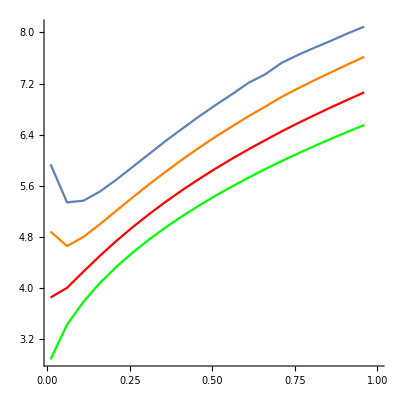

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,3,0.5,0.75μext[1,3,0.5],10]//Abs//Log},{i,0.01,1,0.05}]],
ListLinePlot[Table[{i,βpu[i,0.1,1,3,1.0,0.75μext[1,3,1.0],10]//Abs//Log},{i,0.01,1,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,βpu[i,0.1,1,3,1.5,0.75μext[1,3,1.5],10]//Abs//Log},{i,0.01,1,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,βpu[i,0.1,1,3,1.99,0.75μext[1,3,1.99],10]//Abs//Log},{i,0.01,1,0.05}],PlotStyle->Green],
PlotRange->{{0.01,1},All},AxesOrigin->{0,0},AspectRatio->1
]
```

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point t == 4.61346.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

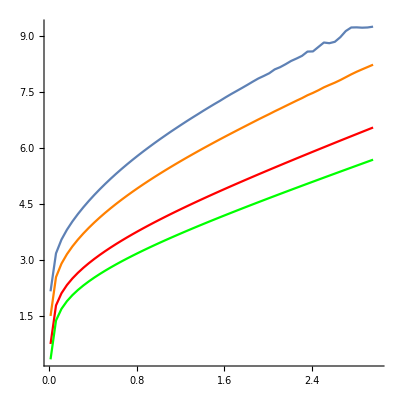

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,2.1,0.50,0.75μext[1,2.1,0.50],10]//Abs//Log},{i,0.01,3,0.05}]],
ListLinePlot[Table[{i,pu[i,0.1,1,2.1,1.00,0.75μext[1,2.1,1.00],10]//Abs//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,pu[i,0.1,1,2.1,1.50,0.75μext[1,2.1,1.50],10]//Abs//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pu[i,0.1,1,2.1,1.74,0.75μext[1,2.1,1.74],10]//Abs//Log},{i,0.01,3,0.05}],PlotStyle->Green],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AspectRatio->1
]
```